```mathematica
SetDirectory[NotebookDirectory[]];
p = Import["video.MOV","ImageList"];
(*p = Import["video.mp4", {"AVI","ImageList"}];*)
```

```mathematica
Length[p]
```

1868

```mathematica
p1 = Show[p[[1000]] ,ImageSize->300, PlotLabel -> "Frame 1000"];
p2= Show[p[[1100]] ,ImageSize->300, PlotLabel -> "Frame 1100"];
p3=Show[p[[1230]] ,ImageSize->300, PlotLabel -> "Frame 1230"];
pp = Deploy@Grid[{{p1,p2, p3}},Dividers->Gray,Spacings->{2,2}]
SetDirectory[NotebookDirectory[]];
Export["rolling_down_frames.eps",pp];
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
BallPositions = ImageFeatureTrack[p[[1000;;1230]], MaxFeatures->1]; (* takes a long time to compute *)
```

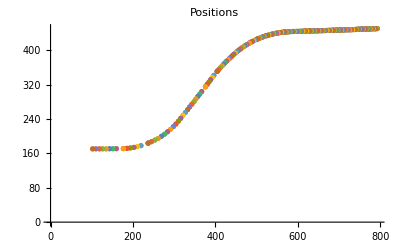

```mathematica
pPos = ListPlot[BallPositions, ImageSize->400,PlotLabel -> "Positions"]
Export["rolling_down_positions.eps",%];
```

Lenght before removal of duplicates is: 231

Lenght after removal of duplicates is: 215

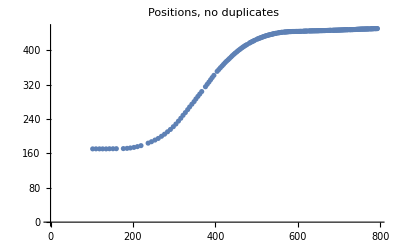

```mathematica
(* Remove records which have the same x *)
(* add frame number first, to keep information about time*)
PositionsWithTime = MapThread[Flatten/@Thread[{##}]&,{BallPositions,Range[1, Length[BallPositions]]}] [[All, 1]];

"Lenght before removal of duplicates is: " <>  ToString[Length[PositionsWithTime]]
(* remove duplicates *)
PositionsWithTimeNoDuplicates=Union[PositionsWithTime,SameTest->(#1[[1]]==#2[[1]]&)]; 
"Lenght after removal of duplicates is: " <>  ToString[Length[PositionsWithTimeNoDuplicates]]

(* separate back into time and coordinates *)
time =PositionsWithTimeNoDuplicates[[All, 3]];
coord = PositionsWithTimeNoDuplicates[[All, {1, 2}]];
pCoord = ListPlot[coord, ImageSize->400,PlotLabel -> "Positions, no duplicates"]
Export["rolling_down_no_duplicates.eps",%];
```

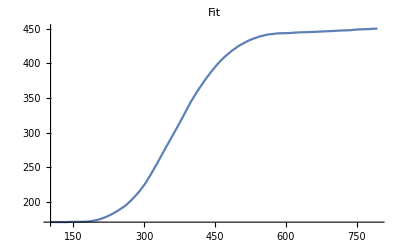

```mathematica
(* if smooting needed 
smothed = MovingAverage[coord, 2] ;
  ListPlot[smothed]
ff= Interpolation[smothed];
*)

ff6= Interpolation[coord];
Minx = Min[coord[[All, 1]]];
Maxx = Max[coord[[All, 1]]];
pFit = Plot[ff6[x], {x, Minx, Maxx}, ImageSize->400, PlotLabel -> "Fit"]
Export["rolling_down_fitted.eps",%];
```

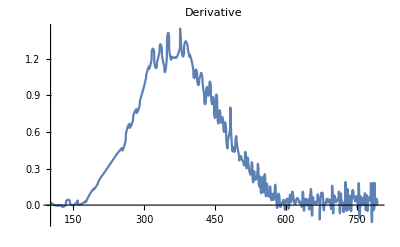

```mathematica
(* Derivative *)
pDer = Plot[ff6'[x], {x, Minx, Maxx}, ImageSize->400, PlotLabel -> "Derivative"]
Export["rolling_down_derivative.eps",%];
```

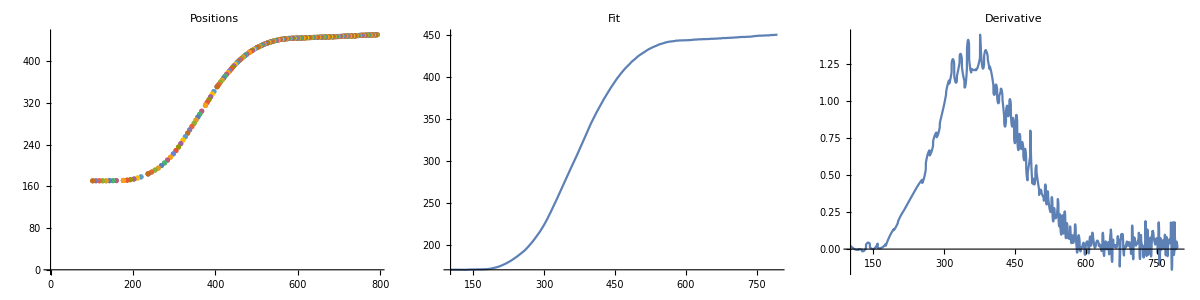

```mathematica
ptotal = Deploy@Grid[{{pPos,pFit, pDer}},Dividers->Gray,Spacings->{2,2}]
Export["rolling_down_positions_and_fit.eps",%];
```